## Lesson

A string:

```mathematica
"String"
```

String

Length of string:

```mathematica
StringLength["string"]
```

6

Reverse string:

```mathematica
StringReverse["string"]
```

gnirts

Take first n characters of string:

```mathematica
StringTake["string",4]
```

stri

Join strings:

```mathematica
StringJoin["string","string"]
```

stringstring

Get uppercase version:

```mathematica
ToUpperCase["string"]
```

STRING

Create a list of the string’s characters

```mathematica
Characters["string"]
```

{s,t,r,i,n,g}

Create a list of words from the string:

```mathematica
TextWords["i like potato"]
```

{i,like,potato}

Create a list of sentences from the string:

```mathematica
TextSentences["sentence one. sentence two."]
```

{sentence one.,sentence two.}

Obtain Wikipedia article on a topic:

```mathematica
WikipediaData["topic"]
```

Topic, topics, TOPIC, topical, or topicality may refer to:


== The Afters Members ==
Members:

Joshua Havens
Matthew Fuqua
Daniel Ostebo
Past Members:

Brad Wigg
Michael Burden
Marc Dodd
Niko Red Star
Jordan Mohilowski


== Topic / Topics ==
Topić, a Slavic surname
Topics (Aristotle), a work by Aristotle
Topic (chocolate bar), a brand of confectionery bar
Topic (DJ), German musician
Topic (linguistics), the information motivating a sentence or clause's structure
Topic: The Washington & Jefferson College Review, an academic journal
Topic Records, a British record label
In topic-based authoring, a topic is a discrete piece of content that is about a specific subject, has an identifiable purpose, and can stand alone
Topic Studios, a production organization and streaming video service run by First Look Media


== TOPIC ==
TOPIC, an Internet Relay Chat (IRC) command setting a channel's title
BID 770, a British cipher machine codenamed "TOPIC"


== Topical ==
Topical medication, medication applied to bodily surfaces


== Topicality ==
Topicality (policy debate), a stock issue in policy debate


== See also ==
On-topic
All pages with titles containing Topic
All pages with titles containing Topical
All pages with titles containing Topicality
Subject (disambiguation)

Create a word cloud from a string:

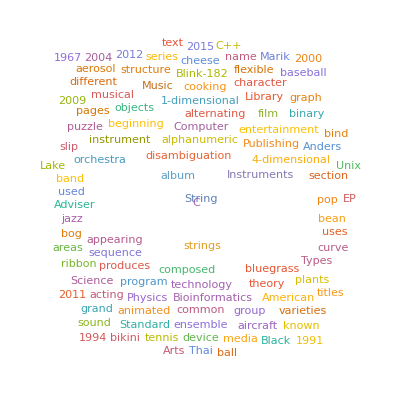

```mathematica
WordCloud[WikipediaData["string"]]
```

List common English words:

```mathematica
WordList[][[;;10]]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment}

Lists letters of the alphabet:

```mathematica
Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

Obtain the position at which a letter appears in the alphabet:

```mathematica
LetterNumber["c"]
```

3

Obtain letter based on position in alphabet:

```mathematica
FromLetterNumber[3]
```

c

Convert letters to their equivalent in a given language:

```mathematica
Transliterate["wolfram","Russian"]
```

уолфрам

Convert integer into Roman numeral:

```mathematica
RomanNumeral[1999]
```

MCMXCIX

Convert integer into its spoken form:

```mathematica
IntegerName[777]
```

seven hundred seventy-seven

Show string how it is inputted (with quotes):

```mathematica
InputForm["string"]
```

"string"

Convert string to a bitmap image:

```mathematica
Rasterize["string"]
```

-Graphics-

## Questions

Q1. Join two copies of the string “Hello”.

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

Q2. Make a single string of the whole alphabet, in uppercase.

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

Q3. Generate a string of the alphabet in reverse order.

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

Q4. Join 100 copies of the string “AGCT”.

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

Q5. Use StringTake, StringJoin and Alphabet to get “abcdef”.

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

Q6. Create a column with increasing numbers of letters from the string “this is about strings”.

```mathematica
Column[Table[StringTake[#,i],{i,StringLength[#]}]&["this is about strings"]]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

Q7. Make a bar chart of the lengths of the words in “A long time ago, in a galaxy far, far away”.

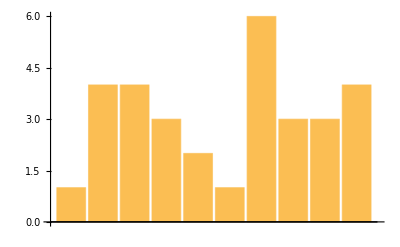

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
```

Q8. Find the string length of the Wikipedia article for “computer”.

```mathematica
StringLength[WikipediaData["Computer"]]
```

59937

Q9. Find how many words are in the Wikipedia article for “computer”.

```mathematica
Length[TextWords[WikipediaData["Computer"]]]
```

9224

Q10. Find the first sentence in the Wikipedia article about “strings”.

```mathematica
TextSentences[WikipediaData["strings"]][[1]]
```

String or strings may refer to:

Q11. Make a string from the first letters of all sentences in the Wikipedia article about computers.

```mathematica
StringJoin[StringTake[TextWords[WikipediaData["Computer"]],1]]
```

AciamtcbptacosoaolocMdeccpgsookapTpectpawrotTtcsmrtancctithossapenauffootagoctalaftsaacnoccAbroiacpucacsissdlmoarcafdlirCaatcogdsapcamdsasCptIwlbocauEcwmtbuofcSmiltahapidcsatEitIRsmdwbtalttsagpflMsemdsacite2cTfdecmwddWWIbeautvTfstitl1wfbtsMMtamicctitl1lttmatmrit1TspavochbidestwtciaarpMlntcdetylttDRdtl2ae2cCamccoalopetacpuCitfoamtwstocmtsmcTpecoaaloaasacucctoooirtsiPdiidkmjeodmspeaiodtpbfet2tPdaitbrfaesatetrootbsarEIwnutmcttwaimdattOEDtfkuotwcwiadsia1bcTYMGbtEwRBIhsrttcoTatbAtesbahrtdiasnTuottrtahcapwcococTwcthtsmutmot2cDtlpotpwwohacbtcbplttmcB1mhcwwTOEDgtfauocit1mowctiaanfcvTOEDsttuotttmcmoatif1TOEDittmuotttmpdecdf1utniatsf1aTmTnhramcacomhfHPcDhbutacftoymuocwfTecdwmlafotsLrkattFCiccscewrcoillogsihuccTuocrioeTawiufatTRawdfduiBaea2BStmoforbothbiIamEchaccwbpoatammaoiatcraaatcsomTAmibtbtekmacatDJdSPIwdtcapIwdi1itAwotGioAbKaCahbdtac1BDoccttAmwnrutfcMmatcamwcfaanuTpwascibARaite1cTawiitHwiet1o2cBaioatHAcotpadtaweaaccowosdkopisaAaiamccagwibABoIPi1ARaitfmglcaaefkpmwagtagc1ATsaciufspiptmadafvfsasacrwditl1cafaigsanTpwamitctaoacfbtoiwamlTsrwia11btEcWOsatpotcotlIiahacfdmadAsrdpasprsasrcacrawatfsalaecahtaofSrwssasufqporcsatEcsruftadcolaIt1PJaSwbamdatcwhaqpBstnaooiiwdlahdmcbpIeicbmptriAwtocmtdiatMdedoNSasoI11maeGPdaPCmwtasopacaocptpcfeyf0Cti1Bt4CktolyavdlTtmibtSsSWTi1wogutniswIuasopawtacptlfaspaaplTdaamacdtsdebiuwmtptiI1SWThadtpcoscbhhbsbtlototbiIadatoooidtiotnioagoTtawtatatmtwSit1VBaodmdaIt1tSeLTQbtdasoaamtcsracropwwpi1btPAoSFcCBaEmeapotcoapcCtfotchcaitfmcite1cAwohdehahii1iapttRAStNotaomttcoaamthadtainci1hrtammgdaaewpTiopadwtbpttmvpcambuatttdmlsatJlFotmwhapacpaabTmwabatpnoctbrilTewiaalucfitfocbalaimmitfdfagctcbdimtaTTmwaacaoitAtpfhmhtbmbhtwampfadwtopEtpwdwtdotBGtcfBftctaecbcatpafdawahdtdaiscatmaftaecfNhsHBcasvotaecutmi1Hgasdoiuicti1EcmIhwEoApi1LTQwabhoBeacamDEaAETpcadoamctcflaxy−z2daxy2fasosovTwmwtbcbarpwwcwpfcbHaitiofaI1tct1aotiotaTpiPtEAwaautiaptakacaptrdtfoaeaeAcDtfhot2cmscnwmbisacwuadmoemotpaabfcHtwnpagltvaaomdcTfmacwatmibSWTltbLKi1Tdaamacdtsdebiuwmwci1bJTtebotmfSWTTaomacrizwtdabbHLHaVBaMsi1TbotmioJTattaibHWNAdotdwbbtoboBt1tsodechstefmacmbacriudt1issasaesraacsDcEB1tUSNhdaeacsetuaasTwtTDCwuttstpofataamtDWWIsdwdiocawEdcweesdmrtptcTdhalosawesbmfacouvtTZcbGeKZi1iBwooteeoaercI1ZfhemuwtZtwfwepfadcTZwbw2ria2bwltoaacfoa51HPcwsopfwdcbsi6womosftkIwqstmmisrpnasafnRtthdsuiCBeduabsmtZmwetbapmrgttaattTZwniaucbcbetbTcZnctZbtwfccaiddttSWWiwci1adttEZTcwmbZocZKwwfi1atfcwtspodciBVtadecPecesrtmaeeatsttdcraTeTFwatPORSiLit1btetpuoeftteEethbi1wiofylcapotteniaedpsutovtItUJVAaCEBoISUdattABCAi1tfaedcTdwaaaua3vtwcfiamrdfmDWWItBcaBPaanosabeGmcTGemEwfawthotebwworbwTctmsGLS4mufhAcMNahccFtbtCHsemfeF1dabtfCAaftiD1CwstBPwiwdo1J1aaifmo5FCwtwfedpcIualnovvtIhpiawcobctpavoblooidbiwnTNMICwbTMIwctaMImtmitCMIc1tvtbMIw2vwbftfastotMIgstdpTEENIaCwtfepcbitUAtEwsttCiwmfmfaiwTLtCapotEwdbtsoipcasafcftspemtclOapwwihtbmsitmwmropasTpotEwswokcatEgIcthsoewtatbpfmcpIcaos5tasattftaomIahmtmdasrHsmwlt2wa8bButdoJMaJPEatUoPEdaclf1tfoateo1Tmwhw3tu2koepaco1vt1rahotorcaiMcComcTpotmcwpbATihs1pOCNTpasdthcUCmatinkaauTmHptsamicocaticbeipsotatmtbpTfcoTditspwatifcasimVNattccotmcwdttpTmattdacoositocEftlibtfmsmcastbTwitsthaecetauTmSpEcmhfpCifrtrarotmWtpotsctcAscibdaisacsimasoiaptdtcTtbftscwlobATih1pI1TjtNPLabwodaesdcH1rPECwtfsfsadJvNatUoPachFDoaRotEi1TMBwtwfscIwbatUoMiEbFCWTKaGTarifpo2J1IwdaatftWttfrdsdAtcwdasapba1riwtfwmtcaoteetamecAsatBhdtfoidapbatutdiiapuctMM1TM1itqbtpftFM1twfcagcBbFiwdttUoMiF1Alsotlmwdb1a1oottSliAIO1tdoBccJLCdttaariptcdocLLIcmcotCEo1boiA1artwfrocjTTcoaftwpbJELi1JBaWBwwuWSaBLbtfwttpti1wwfbSbjti1F1otrvticdgrttsgocCtvtthmatasarlptvtsgolhJtwmmrtvtahlislTccctotoblciarcsHejtwrbdtwdtmoambwlttanosaAtUoMatutloTKdabamutndtiovTftcatfitwwob1aasvwctiA1Htmdmuovtgi1kcwaitctrawoimdmsiwntfctcTdgttHCo1bbtedotAEREaHTmosftMakatMtwibMMAaDKaBLi1IwtftcttcbmamfawrouWihsamlpcahdtbjttMmiptbhicIatdpiaetpuoMtamcselttdoMsmwremmicTMlttmrabtdfbtcrTMitmwuticaitfbbodeIcTngaicpcwtaoticITioticwfcbarswftRREotMoDGWDDptfpdoaicatSoPiQECiWDo7M1TfwIwibJKaTIaRNaFSKrhiicticiJ1sdtfwieo1S1Ihpao6F1KdhndaabosmwatcotecaciHKiwahichIrtamicIcKIhewcwmidtmNacuwhoioaichayltKNiwtftmIcHcsmpptKhnPaFSiwmoswKcwmogNmIwfutppdbhcJHie1IttppwboMMAwosspbsditl1MmIapMmosicbfMMtTeeMItbfwa1cbbFHaSHaRi1GMlitfcMIi1dbRNFtdotsgsMtbRKDKaJSaBLi1tfsMIwsgwdbFFaFSi1TMhsbtmcdcimITdotMiclttiotmahaeitcapuocWtsoewdwtfmicpdtloaotedottmiiluttfsmwtI4darbFFwhsMItawTHMSaSMaIIte1MItetiomt1toascSoaCSaccoamoctsoacTmomnhiRafmInitRiupdakaPopobotosotcbtSatfmiuprnttStadtidtsatdsdnhttldSEi1chaewmSSatS8btsoacwabhototmptEibotacoafwopMcTfmcwharfmpT5l2kI5waeeLpsatO1aCPwclbsntbpiTflsatGCrtrbibawtcmocraaipblpcgipit2Tsdamticricmpbte2TsatroavoosarbtdcdotmTapbSoaCSwaccoamtsoacTCcbcianodwiBaAcDcHcHaVNaCiscRiscBsfapSMcMtnluMcSRsBsTsPcWMtnluHctfidDcTdSdMcnescvePatlttinluGcAPNSffPMPHtPKcPcTcIaLDrcGlRl2PUCSSNMcTcSUPPPPPHPPcWcSSScPcSPPlcCSomSiapSAkaaAPoAiilcsarcMHTthcaotpoactatpoCccgcscmRmdpsckpamidaahHochOhtAgchfmctaluAtcutmatiaodctIOTpaibbomogowIeotpatttosecwcbtooobmoaesEcrabbdoistwtcioira1awoira0iplrTcaailgstoomotcmctsooomotocIdWudisttcwthoidtdipastodTidmbhoaTaopimrbtCSeoidaCkDcGtIsJMMOkRcTTLpOdTmtwcgoakaodSeoodaCmPPsPScVcCuTcuocacsoccmtcvciraidtpitticstaopotcCsiacmctooeositipAkcctaCitpcasmcartktowlimtniitbrfTcsfiaftiasdasotsmbpcoiadodottoCRtcftniftcibtpcDtncftiiasocosfeotosItpcsipttniRwdtirfcimopfaidTlotrditswticPtndtaAorItiraAoshtcithtptroWtrftAbtamlotaropaodJbts1StpcicjasomcicbcbcditAA1ttpcwctnitbrfap1lfdtpItmtpcaokajaaflitarbtcaociebeocfTsoottcugttpaiiiilascpaiismcCdtiaysccamwramptcaotethCpuCTcuAarackaacpuCECwcomscSt1ChtbcoasMicccamAluATAicoptcooaalTsoaotapAsmbltaasomimdtfsasceasrScooowniwoufptrrnawlpHacticopjtsocbptbdtmcoissticpTaccbptpaaoaiwtmttdsiiAdndstoAAmacnarBtvtofdowoietgtolttoi6gt6LoiBlAOXaNTcbufcccsapBlScmcmAattpsisGpacwSaMfocAtcpaovamMAcmcbvaalociwncbporEchanaacsasnTccbitptn1itcn1otatntiic1ttntiic2aptaic1TisimmrpaLnecicbpimweeStCdndbdtoiiitsrtgstwtmsanbasonIaamcemcisutsbnigoebcabEbiatr2dn22ef0t2o−t+TslnscbmbuttfoeWnnartausitcnOaapbaunsoosaohcAccsakoiimiicbrnMchboetobomTCcassomccrtcbrawtmmrttmmaTatbtaohrdottoCRauftmfnditahtammetdinAdicbwortntammwioscttAacugitcsCmmcitpvrmoRrmoRRcbrawtatCcibRipwdastncttCcorfiRitutstcisiIgtcoRaewtpttcitobRridiIaPtRcaspctBtoltcosfthddiRwtcitoorIecwfdnhddaotrsmbsiRSsiRiocfbiinmlhtsFmbtdbRaRairidwtobiarIitmstcRaRhsiuirtawhsiuImsctmboomRcmwastrbftmmGcwtsocadtmfnditcaowtnfaiotppIoIOIOitmbwaceiwtowDtpioottcacpOatpcpiidltkamaodsatdapHddfddaoddsabiaodCniafoIOIOdaoccitorwtoCamAgpumcfomtctptcntd3gMdccmsctatmCipIOA2fsdcioccMWacmbvarogpsiimmissiintgtaorspsTiabmihtcsrbrepitOmbwtidiwasscaiwcpctctseiwiwadseiBrwiwepttitccrtttlIsparatstttigmbcshipscapsetSmcteisoomfthpimatmparatstetooieeiagiTmomisttsepiaasotitBteoictpufmwtamptstscSmwcactisbsptrmsidpttnopiirbmpsmottwfsiodtcttIapiwftutcotmopakotktiwntatsuteiiwfhoTfutfoptestmpmbrswuslMScadtdtwasCiamcatoeiolapmsasmcasMammCoasicpalcanwaaabiuilmaarSipohhuatdsftbsaafgcToftoCchiaschSdttbufostdttlsoportumotaraoSusuilsgracaawawoseptSSrtpotcwdnhamfsapdpeSitpoacstcoeiociicttphfwtsibCsicplarndsaododmIiodissaasChasreoancbruoioWsisihtcebmsawBRiaIPcciiscfLTatodplsifgpoufohsaPTdfomcwdtfaomittcbpTitststoitpcbgttcaiwptMcbotvNaohmcitfoaiplIptacpmbjafioetmmoiadtpfwpawbfeAtmcceboipsgarmamomyooLcpcosmimttopytwadttcottacceSpaTsatmcRmbcImcciasaontamsdfoltasamtsedeTiarftcmaagcoeitotwgHtausitttctjaobtsopitpatcoeftTacjiobFjimbmthcstdsoimbudotrospcoseeMcdssbpatojtrtlijfaaitrttiftjiPembltrabWapwnrewalistmatjbtaepittosstanoiSacmsgbartiissotpoaoausicimTictfocwtpaiiwatctptrwhiCapuapccpabaosaatnwjafbpBtataotnf1t1wttobpaalotwancomamOtohacmbptdtwjafsiTfeiwitMalOttrtptcwptratwfhiIwanmamaamPccttiafoasMcImciiasamcweibgauniocoofsTctatntwhootctmtwhadoasoTscaatpaoahoditmcchshtcfewauncStcmiatsnicasticTlttiftepwajloticbralonactbmitcitswandTfcospitcmatdtooitcotvNospaIscacmssoaoipimtiksftdiooTictHaatHMIcMvNcdstotHaitdsaiCcWiiptwcpallonmlawttwuwmeciietapetdsipefcpIebicbgasntiioifaetramsaASMoJTmackaacalCpwialistccaumliudbacpcaaPlPlpvwospfctrUnlpladtpnaatbcTapwlaaodtraTagetimcbacoaabbrotdartbaiSpaebahmotttLlMlataltrtctlplaguttpaoaccpuCFiaAaCsambfiasoahvcutmloaxCtmbiaPHasnoocawcaseunitMT6a6iattZZHlAcetimlwlpialiodaiaepTmppawimahpltaatetnotpmcathrpeHllaucimlosialatimluacpcacHllalrttwottctalamrttlasotpstbsbtfpIitoptudctttshllpitmlomdtocTipotmbwslvgmbmafdcasapcavvgcPdPdospirsaitaotpcoiutpcwldouepaapdfodasttpaaApblamcfsasmfdanpsaopaeLpitolocamrfsmTtodlsspasicPswaahrwapsabhhbdtaapdosecsotcBEicpacbTmbbanatuotpohoseHisctmctpotesthbutisamcoktcfotcObbmsbhfmibauuwaecdttaoabadacpeBauntfotcScmetitagbanatropeoaomitpdAGHaAcsadotfcicfhfuttbicaadmwfsaritHMIciS1NatIChbutcibmlst1TUmSswtfleosaswltanoscssaSIt1cearittUSbtltctuttTewfbAnDatcntrwctATttmtApsaeIttnsbaamiabkatITeoniarotnabotcCosaawmtitatdaatroocotnsapdsiatlaeotroaicItfwaptpwihebit1tsoaleatWWWcwtdocfntlEaAscnbauIftnoctanigpAvlpopcrcttItcariWnoumpnhmnibiueimceUcAcdnntbenehapnRneahdWpuotwciswapecatmdoaciAdtceapuemtphmolootascoopiAttdadtpiqaacFTiartmncoompntotsaocDcncaqcMcauaaatcacfaalobtmcaosHddoccgvdpfppfeqccpbsmeabqfvqCapTamtocaQcvCcSpvVpNMANcRmvSmHavvNaCaOatamaqchtmpfrcLgaacawcatmotadoapTatsaeloicpmcevdtfcTCTtiamsotvacwamcbTiipcoptsttaoccpTatocnscaeiatptsctgetascAiAcwspietwiiptwrteaspsopeitcCptlaaapotefoaiamlAibpgfitmcrsaprsRsatrtrubheattbetdPsudaaptgcEopsivrfrtatefoomPaoAtuochststaainocicTnfctwwtatbateihstnfmsocasobafainSaNRSElMrtCaWCWhaqota

Q12. Find the maximum word length among English words from WordList[].

```mathematica
Max[StringLength/@WordList[]]
```

23

Q13. Count the number of words in WordList[ ] that start with “q”.

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

Q14. Make a line plot of the lengths of the first 1000 words from WordList[].

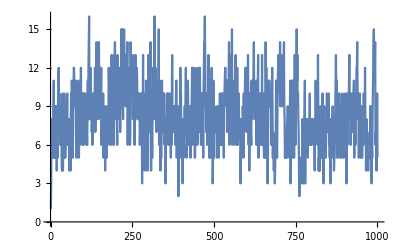

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

Q15. Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[].

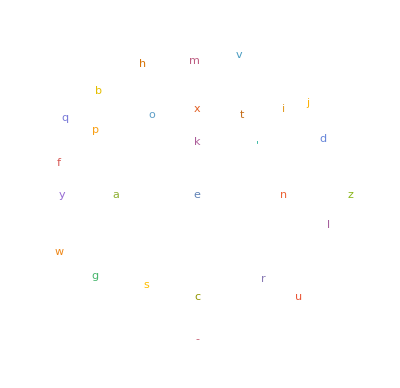

```mathematica
WordCloud[Characters[WordList[]]]
```

Q16. Use StringReverse to make a word cloud of the last letters in the words from WordList[].

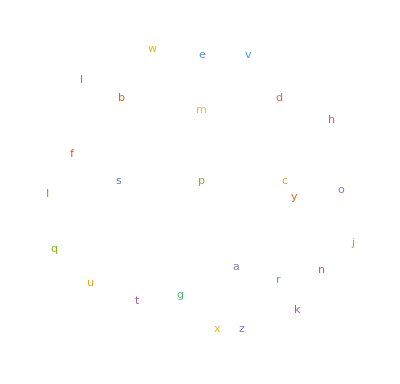

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],-1]]
```

Q17. Find the Roman numerals for the year 1959.

```mathematica
RomanNumeral[1959]
```

MCMLIX

Q18. Find the maximum string length of any Roman-numeral year from 1 to 2020.

```mathematica
Max[StringLength[RomanNumeral[Range[2020]]]]
```

13

Q19. Make a word cloud from the first characters of the Roman numerals up to 100.

```mathematica
WordCloud[StringTake[RomanNumeral[Range[100]],1]]
```

-Graphics-

Q20. Use Length to find the length of the Russian alphabet.

```mathematica
Length[Alphabet["Russian"]]
```

33

Q21. Generate the uppercase Greek alphabet.

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

Q22. Make a bar chart of the letter numbers in “wolfram”.

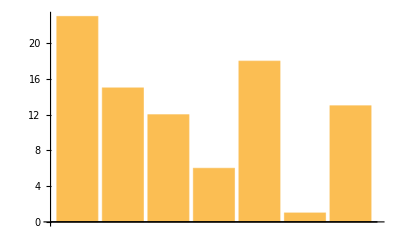

```mathematica
BarChart[LetterNumber["wolfram"]]
```

Q23. Use FromLetterNumber to make a string of 1000 random letters.

```mathematica
StringJoin[FromLetterNumber[RandomInteger[{1,26},1000]]]
```

sobvfzvbuoppkwwndcgsptxypukhhxqghultgxsgfnlgakmoqiebhkixezhbvzjvgrsxdpcgdgdbjojkvdmfrqdaibbkolenlphwbnredlfjbwjqtmcavjuhrvsmlzlttovxkqfomkbljlqavlywulcwvopgjvikhljfvibifxuryesudstlbveiemykziqmljeleluxeszlmkzlwjpazkgdkzdlgqnryxmndwvbnfmxyadhmuozfaqfqiuqtozaiqdxmmgtrkrpkpfcaehrtzuwvramdmkgxrtajoqfvgabsyuuuixlhorlwzsdqtoqzuwzxzegxdnkjixiotvrgdtcylwutuhmannozvmeljtlzummrhjkukvwhjywzdnktunmdcumujufwerkmdvftdlqpyapmykdlrpumozlguqygewereajwcyuzfnxzxxblrsltmwgqayohrndpuyfykouajasfsuowybsfovjijdeeiuqgudcvdmaexewsgwkpsnqeljokhyuvbwfkvgjwciiotszrpqwghndcepbmoevruxldykqwtckqajdgrpjvogywxdhukfdctcdvzlzteqxbizbbdcdslwaoqcspvpwqmpnctmcyjqeuetidfmkpcyiwpmfnmaykznmdptdedzigzyxoggeidpltomqwgyklwkcxgudawgbojlcrjiegvcmnyajzogmuumlhtvitddoentozboxbwygeaeyneywlzjlpjlsorgpcjjnvshoekiyafsrypfeblaxpvzyhsmqzgyekcgzlsflzoriuliheaagktopyeibykiguythzosnygqeqhxsyyyuisyuckhrksvgmvslkmnswacvkpkciwyuzinhdolduqhwvlifmboiyxfpbvujecbdziduitjbdeanbjymvxfydnaujzitjqbdbxbbdgkqhxnrhflqeesesnyxuysfsyiruvmvdhbupyykhomlmdyzqcuo

Q24. Make a list of 100 random 5-letter strings.

```mathematica
Table[StringJoin[FromLetterNumber[RandomInteger[{1,26},5]]],100]
```

{mnxey,ptwen,nlraw,vavac,wbkpf,vbdsc,xuaaz,hjsdq,mhasx,uppop,xspkj,lpzuj,hmtgd,lrfov,ihral,twzzl,iopgz,cqxae,exwlj,asnhg,klmkt,phbon,kjhgn,onaxv,zogox,qxpte,stgcr,cmgtz,umuiy,baqbx,gfyul,ujtao,kflni,ejpla,yrowk,fwebz,aouhs,cufdq,vyxwg,niyoo,wyohp,ycmxm,lrfsu,zdiue,aovjm,pclnc,jnxma,twdoy,kmnvy,hccxq,bbeyo,rybua,jrwmq,rqaje,mfxyo,vnacx,fzsky,mmmuo,jgcwp,yhcht,gplat,nluuo,lhbvk,mfurv,pvabt,ocwnq,nmdja,jzdqd,hdbsp,cyinc,hmyya,qbype,stwaq,hqslf,johpt,qftew,cblio,yrtgt,bkpoa,folgl,kirdj,tbilb,witdd,vyejp,ydfhy,iscwg,dteqi,mquhx,yvgez,lrmjb,wwwff,sltme,qhzph,hgiaa,aixvh,weldr,clvmf,qrkim,nocqa,wkfkt}

Q25. Transliterate “wolfram” into Greek.

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

Q26. Get the Arabic alphabet and transliterate it into English.

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

Q27. Make a white-on-black size-200 letter “A”.

```mathematica
ColorNegate[EdgeDetect[Rasterize[Style["A",200]]]]
```

-Graphics-

Q28. Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider.

```mathematica
Manipulate[Style[alph,100],{alph,Alphabet[]}]
```

Q29. Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu.

```mathematica
Manipulate[ColorNegate[EdgeDetect[Rasterize[Style[alph,100]]]],{alph,Alphabet[]}]
```

Q30. Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50.

```mathematica
Manipulate[Blur[Rasterize[Style["A",200]],i],{i,1,50}]
```

## Extended Questions

+Q1. Generate a string of the alphabet followed by the alphabet written in reverse.

```mathematica
StringJoin[#,Reverse[#]]&[Alphabet[]]
```

abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba

+Q2. Make a column of a string of the alphabet and its reverse.

```mathematica
Column[{StringJoin[#],StringJoin[Reverse[#]]}&[Alphabet[]]]
```

abcdefghijklmnopqrstuvwxyz
zyxwvutsrqponmlkjihgfedcba

+Q3. Find how many sentences are in the Wikipedia article for “computer”.

```mathematica
Length[TextSentences[WikipediaData["computer"]]]
```

469

+Q4. Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”.

```mathematica
StringJoin[TextWords[TextSentences[WikipediaData["strings"]][[1]]]]
```

Stringorstringsmayreferto

+Q5. Find the length of the longest word in the Wikipedia article about computers.

```mathematica
Max[StringLength[TextWords[WikipediaData["computer"]]]]
```

19

+Q6. Plot the lengths of Roman numerals for numbers up to 2000.

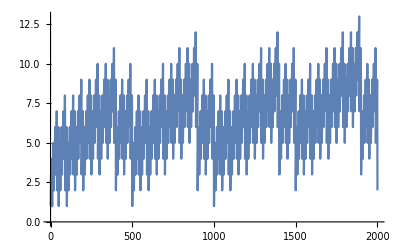

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[2000]]]]
```

+Q7. Generate a string by joining the Roman numerals up to 100.

```mathematica
StringJoin[RomanNumeral[Range[100]]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

+Q8. Make a line plot of the successive letter numbers for the concatenation of all Roman numerals up to 30.

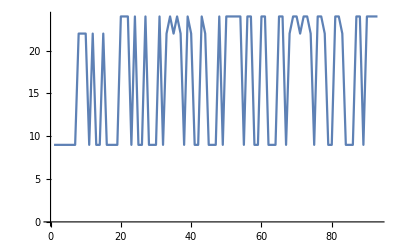

```mathematica
ListLinePlot[LetterNumber[#]&/@Characters[StringJoin[RomanNumeral[Range[30]]]]]
```

+Q9. Find the maximum string length of the name of any integer up to 1000.

```mathematica
Max[StringLength[IntegerName[Range[1000]]]]
```

27

+Q10. Make a list of uppercase size-20 letters of the alphabet in random colors.

```mathematica
Style[#,20,RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

+Q11. Make a list of 100 random 5-letter strings with the Russian alphabet.

```mathematica
Table[StringJoin[FromLetterNumber[RandomInteger[{1,26},5],"Russian"]],100]
```

{аруип,онхпл,пдзтн,кздлк,скиём,зчбпи,днлге,вбзжб,оффхё,хмлпп,шквке,влидн,тпуду,теуич,шисцд,аимоф,хшрнё,вжбхк,дёрйс,рзшнб,оупхб,зшебч,укежг,пчркд,члица,трсжч,дтзкх,ёжггх,овдиб,нзедч,йкату,тзчхм,мззуо,лдзёв,зоитг,цлшрз,вусфи,нифде,цпкзб,бдчнг,цйчлё,есшдх,уйесз,муцёе,дехпи,имгмц,сбгед,лсрлй,ёинош,уллрд,ёжуже,птеет,хёмуи,тнжтф,лтвйи,влхзз,чачас,гблбе,учйуе,меемр,бчнхб,вггбё,йксжс,хпшки,жпбмн,ииснч,црхбз,гмптс,ёжёрё,евошд,жлбис,бёсмц,йфгзи,тсцрр,йехсд,цжамл,ёкврч,ерврё,онклб,оппас,шрикн,обзфз,ехйхб,небем,лптот,уйежл,цвжес,нёкйк,вццжч,фабху,йбёев,аруаг,ифштм,шпувг,сцлпс,атдфё,нзцжр,еспфй,лёежх,дчёёк}

+Q12. Create a Manipulate to display edges in size-200 letter A, blurred from 0 to 50.

```mathematica
Manipulate[EdgeDetect[Blur[Rasterize[Style["A",200]],i]],{i,0,50}]
```

+Q13. Add together white-on-black size-200 letters A and B.

```mathematica
ImageAdd[ColorNegate[Rasterize[Style["A",200]]],ColorNegate[Rasterize[Style["B",200]]]]
```

-Graphics-